## Config

```mathematica
xeq = r*(1-x-y)*s*(x+q*(1-x-y))-x*(1-s)*(y+(1-q)*(1-x-y));
yeq = r*(1-x-y)*(1-s)*(y+(1-q)*(1-x-y))-y*s*(x+q*(1-x-y));
genericEigen = Eigenvalues[{
{D[xeq, x], D[xeq, y]},
{D[yeq, x], D[yeq, y]}
}];
```

```mathematica
mu = 0.02;
xeq = mu*(1-x-y)*s*(x+q*(1-x-y))-c*(1-mu)*x*(1-s)*(y+(1-q)*(1-x-y));
yeq = mu*(1-x-y)*(1-s)*(y+(1-q)*(1-x-y))-c*(1-mu)*y*s*(x+q*(1-x-y));
genericEigen = Eigenvalues[{
{D[xeq, x], D[xeq, y]},
{D[yeq, x], D[yeq, y]}
}];
```

## Symmetric solution example

Let’ s explore the solutions based on the value of c. 
The first two actually lead to y = 1 so we’ re not interested in those, and the next 2 feature x=1, so same thing.
The interesting solutions are then 5th and 6th, let’s see what value they give for the range of c values they’re defined for:

```mathematica
symSol = Solve[{xeq==0, yeq==0}/.{q->0.5, s->0.5}, {x, y},NonNegativeReals]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{x→ConditionalExpression[0, 0.5<r<1.],y→ConditionalExpression[-0.5/(-1.+r)-0.5 √((1.-4. r+4. r^2)/(-1.+r)^2), 0.5<r<1.]},{x→ConditionalExpression[0, 0<r<0.5||r>1.],y→ConditionalExpression[-0.5/(-1.+r)+0.5 √((1.-4. r+4. r^2)/(-1.+r)^2), 0<r<0.5||r>1.]},{x→ConditionalExpression[1., r>1.],y→ConditionalExpression[√(1/(-1.+r)^2)-1./(-1.+r), r>1.]},{x→ConditionalExpression[1., 0<r<0.5||0.5<r<1.],y→ConditionalExpression[-1. √(1/(-1.+r)^2)-1./(-1.+r), 0<r<0.5||0.5<r<1.]},{x→ConditionalExpression[r/(1.+2. r), r>1.],y→ConditionalExpression[(0.5 (-1.-(1. r)/(1.+2. r)))/(-1.+r)+0.5 √((1.-4. r+4. r^2+r^2/(1.+2. r)^2-(4. r^3)/(1.+2. r)^2+(4. r^4)/(1.+2. r)^2+(2. r)/(1.+2. r)+(8. r^2)/(1.+2. r)-(8. r^3)/(1.+2. r))/(-1.+r)^2), r>1.]},{x→ConditionalExpression[r/(1.+2. r), 0<r<0.5||0.5<r<1.],y→ConditionalExpression[(0.5 (-1.-(1. r)/(1.+2. r)))/(-1.+r)-0.5 √((1.-4. r+4. r^2+r^2/(1.+2. r)^2-(4. r^3)/(1.+2. r)^2+(4. r^4)/(1.+2. r)^2+(2. r)/(1.+2. r)+(8. r^2)/(1.+2. r)-(8. r^3)/(1.+2. r))/(-1.+r)^2), 0<r<0.5||0.5<r<1.]}}

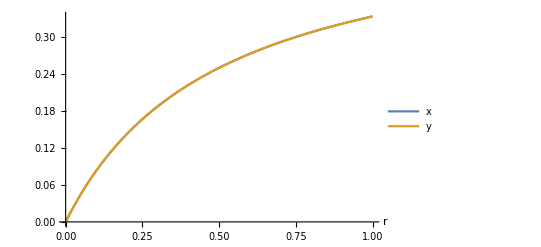

```mathematica
Plot[ {x/.{Normal @symSol[[6]]}, y/.{Normal @symSol[[6]]}},  {r,0, 1},
 PlotLegends->{"x","y"},AxesLabel->Automatic,PlotRange->Full]
```

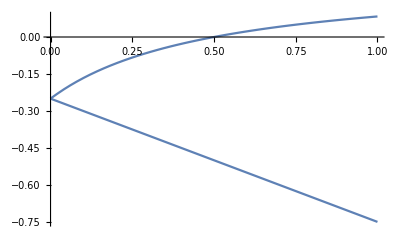

```mathematica
symEigen = Re[genericEigen/.{q->0.5, s->0.5}];
Plot[symEigen/.symSol[[6]] ,{r,0, 1}]
```

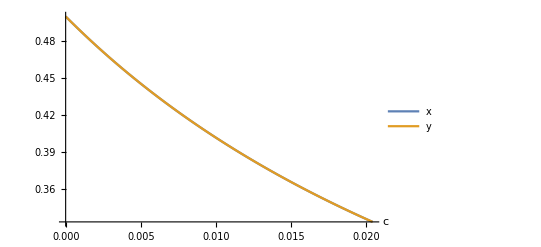

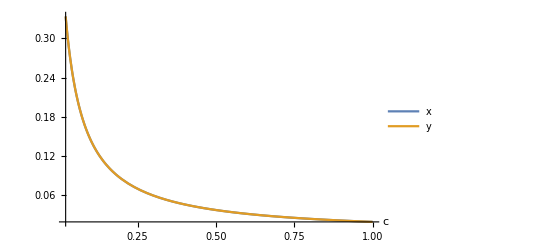

```mathematica
Plot[ {x/.{Normal @symSol[[5]]}, y/.{Normal @symSol[[5]]}},{c,0, 0.0204082},
 PlotLegends->{"x","y"},AxesLabel->Automatic,PlotRange->Full]
Plot[ {x/.{Normal @symSol[[6]]}, y/.{Normal @symSol[[6]]}},  {c,0.0204082, 1},
 PlotLegends->{"x","y"},AxesLabel->Automatic,PlotRange->Full]
```

Stability analysis:

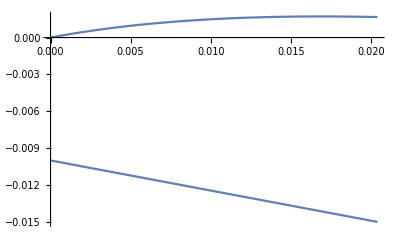

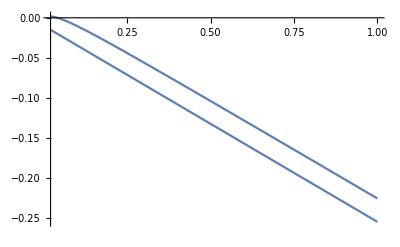

```mathematica
symEigen = Re[genericEigen/.{q->0.5, s->0.5}];
Plot[symEigen/.symSol[[5]] , {c,0, 0.0204082}]
Plot[symEigen/.symSol[[6]] ,{c,0.0204082, 1}]
```

## Asymmetric solution example

```mathematica
asymSol = Solve[{xeq==0, yeq==0}/.{q->0.4, s->0.5}, {x, y},NonNegativeReals]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{x→ConditionalExpression[0, 0<c<0.0204082||c>0.0510204],y→ConditionalExpression[(0.25 (1.+98. c))/(-1.+49. c)+0.25 √((25.-980. c+9604. c^2)/(-1.+49. c)^2), 0<c<0.0204082||c>0.0510204]},{x→ConditionalExpression[0, ],y→ConditionalExpression[(0.25 (1.+98. c))/(-1.+49. c)-0.25 √((25.-980. c+9604. c^2)/(-1.+49. c)^2), ]},{x→ConditionalExpression[1., 0<c<0.0204082],y→ConditionalExpression[61.25 √(c^2/(-1.+49. c)^2)+(61.25 c)/(-1.+49. c), 0<c<0.0204082]},{x→ConditionalExpression[1., ],y→ConditionalExpression[-61.25 √(c^2/(-1.+49. c)^2)+(61.25 c)/(-1.+49. c), ]},{x→ConditionalExpression[(25.-980. c+9604. c^2)/(50.-1225. c-28812. c^2+705894. c^3), 0.0204082<c<0.0340136||0.0340136<c<0.0408163||c>0.0510204],y→ConditionalExpression[(0.25 (1.+98. c-(1. (25.-980. c+9604. c^2))/(50.-1225. c-28812. c^2+705894. c^3)+(147. c (25.-980. c+9604. c^2))/(50.-1225. c-28812. c^2+705894. c^3)))/(-1.+49. c)-0.25 √((25.-980. c+9604. c^2+(25. (25.-980. c+9604. c^2)^2)/((50.-1225. c-28812. c^2+705894. c^3)^2)-(1470. c (25.-980. c+9604. c^2)^2)/((50.-1225. c-28812. c^2+705894. c^3)^2)+(21609. c^2 (25.-980. c+9604. c^2)^2)/((50.-1225. c-28812. c^2+705894. c^3)^2)-(50. (25.-980. c+9604. c^2))/(50.-1225. c-28812. c^2+705894. c^3)+(2450. c (25.-980. c+9604. c^2))/(50.-1225. c-28812. c^2+705894. c^3)+(28812. c^2 (25.-980. c+9604. c^2))/(50.-1225. c-28812. c^2+705894. c^3))/(-1.+49. c)^2), 0.0204082<c<0.0340136||0.0340136<c<0.0408163||c>0.0510204]},{x→ConditionalExpression[(25.-980. c+9604. c^2)/(50.-1225. c-28812. c^2+705894. c^3), 0<c<0.0204082||0.041658<c<0.0440472||0.0440472<c<0.0510204],y→ConditionalExpression[(0.25 (1.+98. c-(1. (25.-980. c+9604. c^2))/(50.-1225. c-28812. c^2+705894. c^3)+(147. c (25.-980. c+9604. c^2))/(50.-1225. c-28812. c^2+705894. c^3)))/(-1.+49. c)+0.25 √((25.-980. c+9604. c^2+(25. (25.-980. c+9604. c^2)^2)/((50.-1225. c-28812. c^2+705894. c^3)^2)-(1470. c (25.-980. c+9604. c^2)^2)/((50.-1225. c-28812. c^2+705894. c^3)^2)+(21609. c^2 (25.-980. c+9604. c^2)^2)/((50.-1225. c-28812. c^2+705894. c^3)^2)-(50. (25.-980. c+9604. c^2))/(50.-1225. c-28812. c^2+705894. c^3)+(2450. c (25.-980. c+9604. c^2))/(50.-1225. c-28812. c^2+705894. c^3)+(28812. c^2 (25.-980. c+9604. c^2))/(50.-1225. c-28812. c^2+705894. c^3))/(-1.+49. c)^2), 0<c<0.0204082||0.041658<c<0.0440472||0.0440472<c<0.0510204]}}

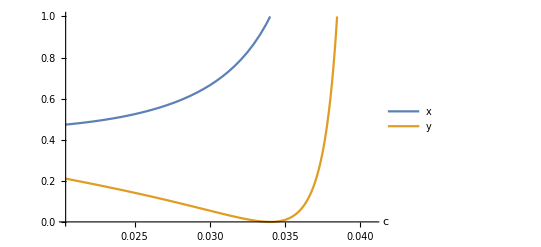

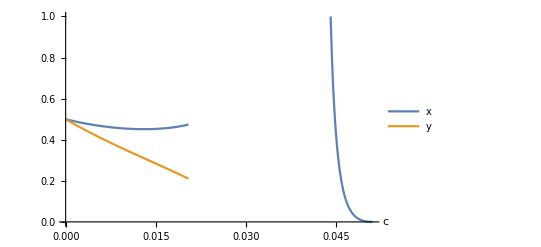

```mathematica
Plot[ {x/.{Normal @asymSol[[5]]}, y/.{Normal @asymSol[[5]]}} , 
{c,0.02040816326530612, 0.0408163}, PlotLegends->{"x","y"},AxesLabel->Automatic,PlotRange->{0,1}]
Plot[ {x/.{Normal @asymSol[[6]]}, y/.{Normal @asymSol[[6]]}} ,
 {c,0, 0.0510204}, PlotLegends->{"x","y"},AxesLabel->Automatic,PlotRange->{0,1}]
```

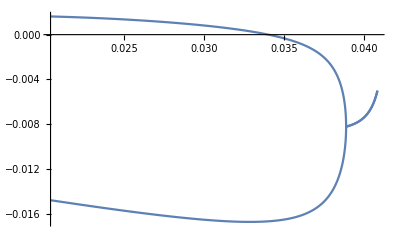

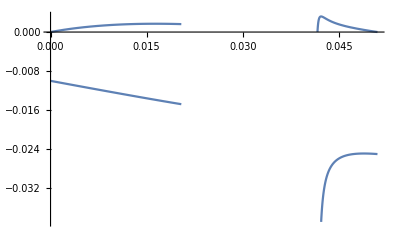

```mathematica
asymEigen = Re[genericEigen /.{q->0.4, s->0.5}];
Plot[asymEigen /.asymSol[[5]], {c,0.0204082, 0.0408163}]
Plot[asymEigen/.asymSol[[6]] , {c,0, 0.0510204}]
```

Only solution 5 can be stable, and starting at c > 0.0340136, which also corresponds to a solution x > 1, which doesn’t make sense. So actually only the solutions for c > 0.0510204 are to be considered.

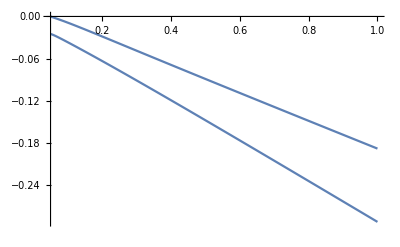

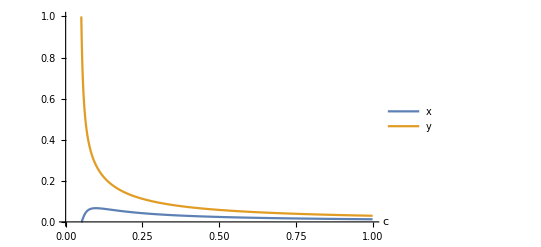

```mathematica
Plot[asymEigen/.asymSol[[5]], {c,0.0510204, 1}]
Plot[ {x/.{Normal @asymSol[[5]]}, y/.{Normal @asymSol[[5]]}} , 
{c,0.0510204, 1}, PlotLegends->{"x","y"},AxesLabel->Automatic,PlotRange->{0,1}]
```

Lower q leads to lower x relatively to y

```mathematica
asymSol2 = Solve[{xeq==0, yeq==0}/.{q->0.5, s->0.4}, {x, y},NonNegativeReals]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{x→ConditionalExpression[0, 0<c<0.0272109||0.0272109<c<0.0306122||c>0.0612245],y→ConditionalExpression[(49. c)/(-3.+98. c)+√((9.-294. c+2401. c^2)/(-3.+98. c)^2), 0<c<0.0272109||0.0272109<c<0.0306122||c>0.0612245]},{x→ConditionalExpression[0, 0.0306122<c<0.0408163||0.0408163<c<0.0442177||0.0442177<c<0.0479751||0.0479751<c<0.0612245],y→ConditionalExpression[(49. c)/(-3.+98. c)-1. √((9.-294. c+2401. c^2)/(-3.+98. c)^2), 0.0306122<c<0.0408163||0.0408163<c<0.0442177||0.0442177<c<0.0479751||0.0479751<c<0.0612245]},{x→ConditionalExpression[1., 0<c<0.0272109||0.0272109<c<0.0306122],y→ConditionalExpression[98. √(c^2/(-3.+98. c)^2)+(98. c)/(-3.+98. c), 0<c<0.0272109||0.0272109<c<0.0306122]},{x→ConditionalExpression[1., 0.0306122<c<0.0408163||0.0408163<c<0.0442177||0.0442177<c<0.0479751||0.0479751<c<0.0612245||c>0.0612245],y→ConditionalExpression[-98. √(c^2/(-3.+98. c)^2)+(98. c)/(-3.+98. c), 0.0306122<c<0.0408163||0.0408163<c<0.0442177||0.0442177<c<0.0479751||0.0479751<c<0.0612245||c>0.0612245]},{x→ConditionalExpression[(36.-1176. c+9604. c^2)/(52.-1176. c-31213. c^2+705894. c^3), 0.0306122<c<0.0408163||c>0.0612245],y→ConditionalExpression[(49. (c+(c (36.-1176. c+9604. c^2))/(52.-1176. c-31213. c^2+705894. c^3)))/(-3.+98. c)-1. √((9.-294. c+2401. c^2+(9. (36.-1176. c+9604. c^2)^2)/((52.-1176. c-31213. c^2+705894. c^3)^2)-(294. c (36.-1176. c+9604. c^2)^2)/((52.-1176. c-31213. c^2+705894. c^3)^2)+(2401. c^2 (36.-1176. c+9604. c^2)^2)/((52.-1176. c-31213. c^2+705894. c^3)^2)-(18. (36.-1176. c+9604. c^2))/(52.-1176. c-31213. c^2+705894. c^3)+(588. c (36.-1176. c+9604. c^2))/(52.-1176. c-31213. c^2+705894. c^3)+(4802. c^2 (36.-1176. c+9604. c^2))/(52.-1176. c-31213. c^2+705894. c^3))/(-3.+98. c)^2), 0.0306122<c<0.0408163||c>0.0612245]},{x→ConditionalExpression[(36.-1176. c+9604. c^2)/(52.-1176. c-31213. c^2+705894. c^3), 0<c<0.0272109||0.0272109<c<0.0306122||0.0442177<c<0.0479751||0.0479751<c<0.0612245],y→ConditionalExpression[(49. (c+(c (36.-1176. c+9604. c^2))/(52.-1176. c-31213. c^2+705894. c^3)))/(-3.+98. c)+√((9.-294. c+2401. c^2+(9. (36.-1176. c+9604. c^2)^2)/((52.-1176. c-31213. c^2+705894. c^3)^2)-(294. c (36.-1176. c+9604. c^2)^2)/((52.-1176. c-31213. c^2+705894. c^3)^2)+(2401. c^2 (36.-1176. c+9604. c^2)^2)/((52.-1176. c-31213. c^2+705894. c^3)^2)-(18. (36.-1176. c+9604. c^2))/(52.-1176. c-31213. c^2+705894. c^3)+(588. c (36.-1176. c+9604. c^2))/(52.-1176. c-31213. c^2+705894. c^3)+(4802. c^2 (36.-1176. c+9604. c^2))/(52.-1176. c-31213. c^2+705894. c^3))/(-3.+98. c)^2), 0<c<0.0272109||0.0272109<c<0.0306122||0.0442177<c<0.0479751||0.0479751<c<0.0612245]}}

```mathematica
range51 = {c,0.030612244897959183,0.04081632653061224};
range52 = {c,0.0612245,1};
range61 = {c,0,0.030612244897959183};
range62 = {c,0.04421768707482993,0.061224489795918366};
```

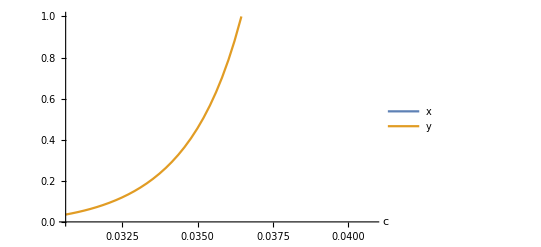

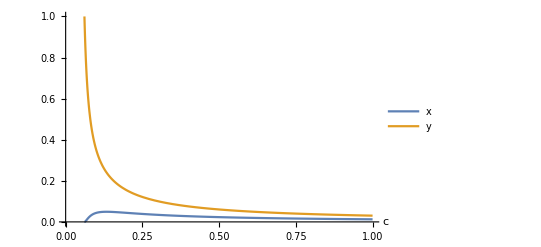

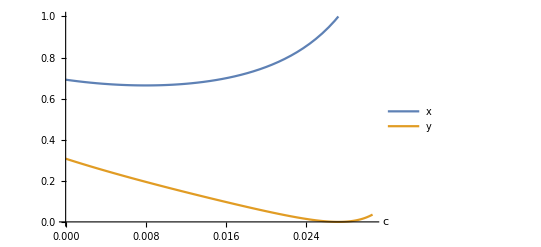

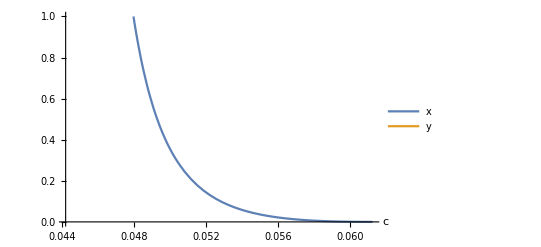

```mathematica
Plot[ {x/.{Normal @asymSol2[[5]]}, y/.{Normal @asymSol2[[5]]}} , 
range51, PlotLegends->{"x","y"},AxesLabel->Automatic,PlotRange->{0,1}]
Plot[ {x/.{Normal @asymSol2[[5]]}, y/.{Normal @asymSol2[[5]]}} , 
range52, PlotLegends->{"x","y"},AxesLabel->Automatic,PlotRange->{0,1}]
Plot[ {x/.{Normal @asymSol2[[6]]}, y/.{Normal @asymSol2[[6]]}} ,
range61 , PlotLegends->{"x","y"},AxesLabel->Automatic,PlotRange->{0,1}]
Plot[ {x/.{Normal @asymSol2[[6]]}, y/.{Normal @asymSol2[[6]]}} ,
range62 , PlotLegends->{"x","y"},AxesLabel->Automatic,PlotRange->{0,1}]
```

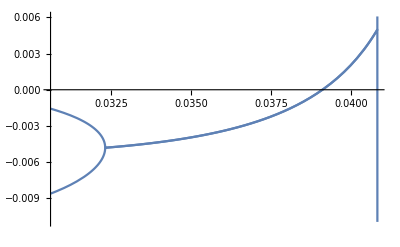

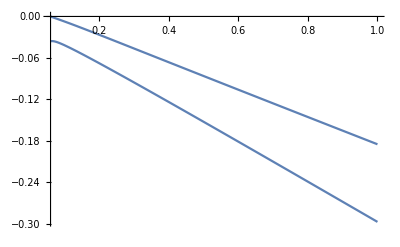

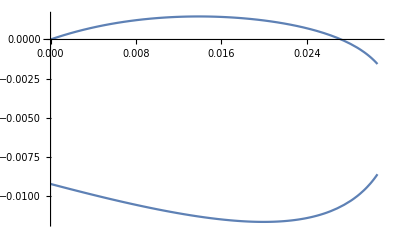

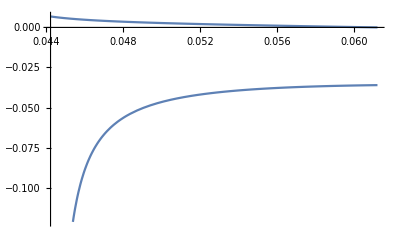

```mathematica
asymEigen2 = Re[genericEigen /.{q->0.5, s->0.4}];
Plot[asymEigen2 /.asymSol2[[5]], range51]
Plot[asymEigen2 /.asymSol2[[5]], range52]
Plot[asymEigen2/.asymSol2[[6]] , range61]
Plot[asymEigen2/.asymSol2[[6]] , range62]
```

```mathematica
asymSol3 = Solve[{xeq==0, yeq==0}/.{q->0.5, s->0.3}, {x, y},NonNegativeReals]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{x→ConditionalExpression[0, 0.047619<c<0.0563654||0.0563654<c<0.0612245||0.0612245<c<0.0952381],y→ConditionalExpression[(10.5 c)/(-1.+21. c)-0.5 √((4.-84. c+441. c^2)/(-1.+21. c)^2), 0.047619<c<0.0563654||0.0563654<c<0.0612245||0.0612245<c<0.0952381]},{x→ConditionalExpression[0, 0<c<0.0174927||0.0174927<c<0.0408163||0.0408163<c<0.047619||c>0.0952381],y→ConditionalExpression[(10.5 c)/(-1.+21. c)+0.5 √((4.-84. c+441. c^2)/(-1.+21. c)^2), 0<c<0.0174927||0.0174927<c<0.0408163||0.0408163<c<0.047619||c>0.0952381]},{x→ConditionalExpression[1., 0<c<0.0174927||0.0174927<c<0.0408163||0.0408163<c<0.047619],y→ConditionalExpression[21. √(c^2/(-1.+21. c)^2)+(21. c)/(-1.+21. c), 0<c<0.0174927||0.0174927<c<0.0408163||0.0408163<c<0.047619]},{x→ConditionalExpression[1., 0.047619<c<0.0563654||0.0563654<c<0.0612245||0.0612245<c<0.0952381||c>0.0952381],y→ConditionalExpression[-21. √(c^2/(-1.+21. c)^2)+(21. c)/(-1.+21. c), 0.047619<c<0.0563654||0.0563654<c<0.0612245||0.0612245<c<0.0952381||c>0.0952381]},{x→ConditionalExpression[(196.-4116. c+21609. c^2)/(232.-4116. c-139258. c^2+2.47063×10^6 c^3), c>0.0952381],y→ConditionalExpression[(10.5 (c+(c (196.-4116. c+21609. c^2))/(232.-4116. c-139258. c^2+2.47063×10^6 c^3)))/(-1.+21. c)-0.5 √((4.-84. c+441. c^2+(4. (196.-4116. c+21609. c^2)^2)/((232.-4116. c-139258. c^2+2.47063×10^6 c^3)^2)-(84. c (196.-4116. c+21609. c^2)^2)/((232.-4116. c-139258. c^2+2.47063×10^6 c^3)^2)+(441. c^2 (196.-4116. c+21609. c^2)^2)/((232.-4116. c-139258. c^2+2.47063×10^6 c^3)^2)-(8. (196.-4116. c+21609. c^2))/(232.-4116. c-139258. c^2+2.47063×10^6 c^3)+(168. c (196.-4116. c+21609. c^2))/(232.-4116. c-139258. c^2+2.47063×10^6 c^3)+(882. c^2 (196.-4116. c+21609. c^2))/(232.-4116. c-139258. c^2+2.47063×10^6 c^3))/(-1.+21. c)^2), c>0.0952381]},{x→ConditionalExpression[(196.-4116. c+21609. c^2)/(232.-4116. c-139258. c^2+2.47063×10^6 c^3), 0<c<0.0174927||0.0174927<c<0.0408163||0.0563654<c<0.0612245||0.0612245<c<0.0952381],y→ConditionalExpression[(10.5 (c+(c (196.-4116. c+21609. c^2))/(232.-4116. c-139258. c^2+2.47063×10^6 c^3)))/(-1.+21. c)+0.5 √((4.-84. c+441. c^2+(4. (196.-4116. c+21609. c^2)^2)/((232.-4116. c-139258. c^2+2.47063×10^6 c^3)^2)-(84. c (196.-4116. c+21609. c^2)^2)/((232.-4116. c-139258. c^2+2.47063×10^6 c^3)^2)+(441. c^2 (196.-4116. c+21609. c^2)^2)/((232.-4116. c-139258. c^2+2.47063×10^6 c^3)^2)-(8. (196.-4116. c+21609. c^2))/(232.-4116. c-139258. c^2+2.47063×10^6 c^3)+(168. c (196.-4116. c+21609. c^2))/(232.-4116. c-139258. c^2+2.47063×10^6 c^3)+(882. c^2 (196.-4116. c+21609. c^2))/(232.-4116. c-139258. c^2+2.47063×10^6 c^3))/(-1.+21. c)^2), 0<c<0.0174927||0.0174927<c<0.0408163||0.0563654<c<0.0612245||0.0612245<c<0.0952381]}}

```mathematica
range51 = {c,0.09523809523809523, 1};
range61 = {c,0,0.04081632653061224};
range62 = {c,0.056365403304178816,0.09523809523809523};
```

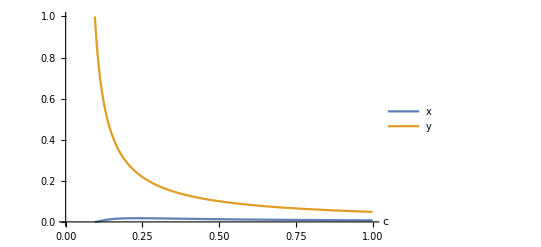

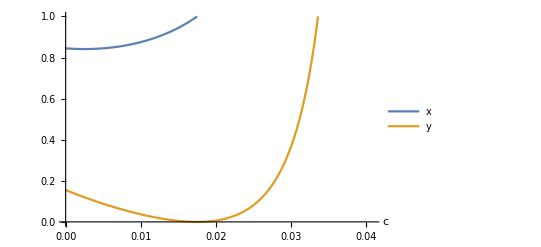

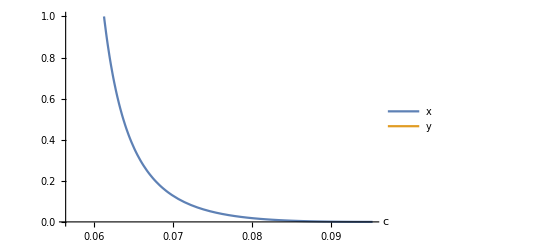

```mathematica
Plot[ {x/.{Normal @asymSol3[[5]]}, y/.{Normal @asymSol3[[5]]}} , 
range51, PlotLegends->{"x","y"},AxesLabel->Automatic,PlotRange->{0,1}]
Plot[ {x/.{Normal @asymSol3[[6]]}, y/.{Normal @asymSol3[[6]]}} ,
range61 , PlotLegends->{"x","y"},AxesLabel->Automatic,PlotRange->{0,1}]
Plot[ {x/.{Normal @asymSol3[[6]]}, y/.{Normal @asymSol3[[6]]}} ,
range62 , PlotLegends->{"x","y"},AxesLabel->Automatic,PlotRange->{0,1}]
```

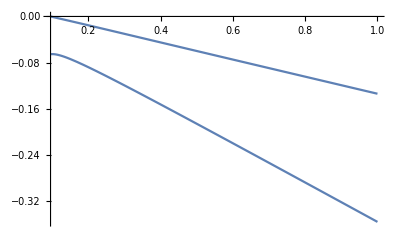

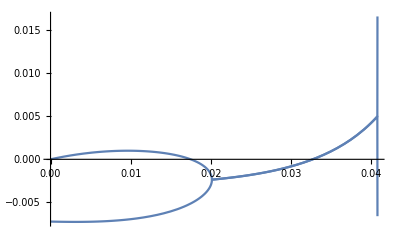

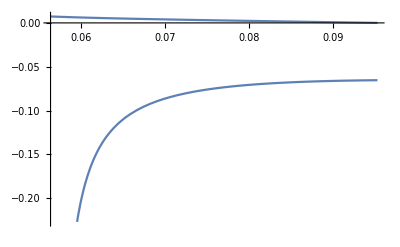

```mathematica
asymEigen3 = Re[genericEigen /.{q->0.5, s->0.3}];
Plot[asymEigen3 /.asymSol3[[5]], range51]
Plot[asymEigen3/.asymSol3[[6]] , range61]
Plot[asymEigen3/.asymSol3[[6]] , range62]
```

## Vector field

```mathematica
texMathStyle={FontFamily->"CMU Serif",FontSize->7*1.5};
texTextStyle = {FontFamily-> "Latin Modern Sans", FontSize->7*1.5} ;
cm=1.38095*72/2.54;
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

Part::partd: Part specification List⟦1⟧ is longer than depth of object.

Part::partd: Part specification List⟦2⟧ is longer than depth of object.

Part::partd: Part specification List⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification List⟦1⟧ is longer than depth of object.

Part::partd: Part specification (-0.02107)⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

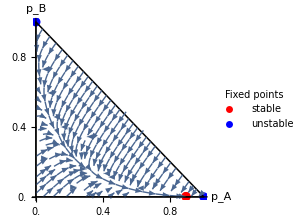

/home/thomas/Documents/PhD/code/metapop-analytical/figs/stream_plot_eq_s=0.57_q=0.45_c=0.05.pdf

```mathematica
numTol = 10^(-10);
params = {s->0.57, q->0.45, c->0.05};
(* Solution limited to Reals and not only positive ones because the result will be numericised by
Mathematica, and there can be a floating point accuracy error making zero solutions negative *)
plotSol = Solve[{xeq==0, yeq==0}/.params, {x, y},Reals];
plotEigen = Re[genericEigen /.params/.plotSol];
valuesSol =  Normal @Table[{x,y}/.plotSol[[i]], {i, 1, Length[plotSol]}];
validIdx = Flatten[Position[
valuesSol,
_?(#[[1]]≥ -numTol && #[[2]]≥ -numTol && #[[1]]+#[[2]]≤ 1+numTol&)]];
stableIdx = Position[plotEigen[[validIdx]], _?(NumericQ[#[[1]]]&& NumericQ[#[[2]]]&& #[[1]] < 0 &&  #[[2]] < 0 &)];
(* Delete cannot take the flattened version because otherwise it deletes an element going in higher dimension. 
 If there is either no stable or unstable solution, we need to replace the corresponding empty list by ∅, 
   because ListPlot can't handle an empty list correctly. *)
p1 = ListPlot[
{valuesSol[[validIdx]][[Flatten[stableIdx]]], Delete[valuesSol[[validIdx]], stableIdx]}/.{}->{∅}, PlotStyle->{Directive[PointSize[0.03],Red], Directive[PointSize[0.03],Blue]}, 
PlotLegends->Placed[PointLegend[{"stable", "unstable"},LegendLabel->"Fixed points", LabelStyle->texMathStyle, LegendMarkerSize->6],
{Scaled[{0.95,0.8}], {1, 1}}]];
p2 = StreamPlot[
{xeq, yeq}/.params, {x,0,1}, {y, 0,1},
RegionFunction->Function[{x,y},x+y≤1 &&x≥0 && y≥ 0],
(* StreamColorFunction-> Automatic,
StreamColorFunction->(ColorData["BlueGreenYellow",Norm[{#1,#2}]]&),
StreamColorFunctionScaling-> False, 
PlotLegends->BarLegend[{"BlueGreenYellow", {0, 1}},LegendLabel->"Norm of the rates"], *) 
(*VectorPoints->Fine,VectorScaling->Automatic,*)
RegionFillingStyle->None, RegionBoundaryStyle->Directive[Black, Thickness[0.005]]];
plot = Show[p1, p2, PlotRange->{{0,1}, {0,1}}, AspectRatio->Automatic, AxesLabel->{Subscript[p, A],Subscript[p, B]}, BaseStyle->texMathStyle,
Ticks->{{#,Framed[#,FrameMargins->-1,FrameStyle->None]}&/@Range[0,1,0.2],{#,Framed[#,FrameStyle->None]}&/@Range[0,1,0.2]},
 ImageSize-> {5.6cm,5.6cm}]
paramsStr ="_s="<>ToString[s/.params]<>"_q="<>ToString[q/.params]<> "_c="<>ToString[c/.params];
fileName = FileNameJoin[{NotebookDirectory[],"figs", "stream_plot_eq"<>paramsStr<>".pdf"}]
Export[fileName,plot, Magnification->1] ;
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"figs", "stream_plot_eq"<>paramsStr<>".eps"}],Show[p1, p2, PlotRange->{{0,1}, {0,1}}, AspectRatio->Automatic, AxesLabel->{Subscript[p, A],Subscript[p, B]}, BaseStyle->texMathStyle,
 ImageSize-> {10cm, 10cm}]]
```

/home/thomas/Documents/PhD/code/metapop-analytical/figs/stream_plot_eq_s=0.55_q=0.45_c=0.05.eps

## General solution

```mathematica
mu = 0.02;
xeq = mu*(1-x-y)*s*(x+q*(1-x-y))-c*(1-mu)*x*(1-s)*(y+(1-q)*(1-x-y));
yeq = mu*(1-x-y)*(1-s)*(y+(1-q)*(1-x-y))-c*(1-mu)*y*s*(x+q*(1-x-y));
genericEigen = Eigenvalues[{
{D[xeq, x], D[xeq, y]},
{D[yeq, x], D[yeq, y]}
}];
```

```mathematica
xeq = r*(1-x-y)*s*(x+q*(1-x-y))-x*(1-s)*(y+(1-q)*(1-x-y));
yeq = r*(1-x-y)*(1-s)*(y+(1-q)*(1-x-y))-y*s*(x+q*(1-x-y));
genericEigen = Eigenvalues[{
{D[xeq, x], D[xeq, y]},
{D[yeq, x], D[yeq, y]}
}];
```

```mathematica
sol = Solve[{xeq==0, yeq==0}, {x, y},NonNegativeReals];
```

We know from before that it’s the solution where the y’s second term is + root(something) that interests us, as it’s the one which can be stable in both the symmetric and asymmetric cases, so here it’s not sol[[6]] but sol[[5]] (no idea how the solutions are ordered)

```mathematica
generalCoexSol = Assuming[r>0 && q<1 && s<1 && s>0 && q>0 && r<1, Simplify@sol[[5]]];
```

```mathematica
boolCoex = FirstCase[x/.generalCoexSol,ConditionalExpression[_,c_]:>c,Missing[],{0,-1}];
eigenCoex = Re@Normal@(genericEigen/.generalCoexSol);
xsolCoex =x/.Normal@generalCoexSol;
ysolCoex =y/. Normal@generalCoexSol;
```

Heatmap for third param??

```mathematica
myBlue = RGBColor[0.37,0.51,0.71];
myOrange = RGBColor[225/255,156/255,35/255];
regionPlot = RegionPlot3D[eigenCoex[[1]] <0 && eigenCoex[[2]]<0 && boolCoex && xsolCoex< 1 && ysolCoex< 1,
{s, 0.01, 0.99}, {q, 0.5,1}, {r, 0.01, 0.5}, AxesLabel->Automatic, BaseStyle->texMathStyle, 
PlotStyle->Directive[GrayLevel[0.62],Specularity[White,100]] , Lighting->"Neutral",
MeshFunctions->{#1&,#2&,#1&,#1&},Mesh->{10,10,{0.5},{0.4}},MeshStyle->{Automatic,Automatic,{Thick,myBlue},{Thick,myOrange}}]
```

-Graphics3D-

```mathematica
options = -Graphics3D-//Options;
```

```mathematica
fileName = FileNameJoin[{NotebookDirectory[],"figs", "coex_region_3D.pdf"}]
Export[fileName,Show[regionPlot, options], ImageSize-> {8cm,8cm}, "AllowRasterization"-> True,ImageResolution-> 600];
```

/home/thomas/Documents/PhD/code/metapop-analytical/figs/coex_region_3D.pdf

```mathematica
pov3Dplot = Graphics[Inset[Show[regionPlot, options],Automatic,Automatic,Scaled[1]], ImageSize-> {8.7cm,8.7cm}]
```

-Graphics-

```mathematica
fileName = FileNameJoin[{NotebookDirectory[],"figs", "coex_region_3D.pdf"}];
Export[fileName,pov3Dplot,"AllowRasterization"->False];
```

The higher r (ie, the slower it is to learn the other lang), the smaller the coexistence region.
The farther q is away from 0.5 (so the higher here), the larger the coexistence region for relatively (>0.2) high values of r.
The weird volume for high values of r correspond to unphysical solution (>1).

```mathematica
symPrestEigen = eigenCoex/.{s->0.5};
symPrestboolCoex = boolCoex/.{s->0.5};
symPrestSolCoex = Normal@generalCoexSol/.{s->0.5};
asymPrestEigen = eigenCoex/.{s->0.4};
asymPrestboolCoex = boolCoex/.{s->0.4};
asymPrestSolCoex = Normal@generalCoexSol/.{s->0.4};
```

```mathematica
coex2DRegionPlot = RegionPlot[{
symPrestEigen[[1]] <0 && symPrestEigen[[2]]<0 && symPrestboolCoex && (x/.symPrestSolCoex) < 1 && (y/.symPrestSolCoex) < 1, 
asymPrestEigen[[1]] <0 && asymPrestEigen[[2]]<0 && asymPrestboolCoex && (x/.asymPrestSolCoex) < 1 && (y/.asymPrestSolCoex) < 1},
{q, 0.5,1},{r, 0.01, 0.5},  FrameLabel->{q, r},AxesLabel->Automatic, Frame->{{True,False},{True,False}},
PlotLegends->Placed[SwatchLegend[{"s = 0.5", "s = 0.4"}, LabelStyle-> texMathStyle], {Scaled[{0.95,0.8}], {1, 1}}],
BaseStyle->texMathStyle,ImageSize-> {7cm,7cm}];
```

```mathematica
fileName = FileNameJoin[{NotebookDirectory[],"figs", "coex_region_2D.pdf"}]
Export[fileName, coex2DRegionPlot];
```

/home/thomas/Documents/PhD/code/metapop-analytical/figs/coex_region_2D.pdf

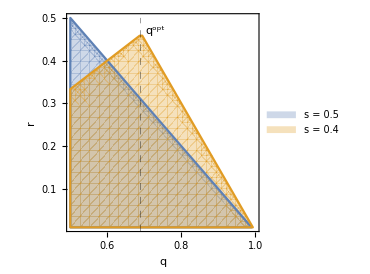

```mathematica
line = ContourPlot[q== 0.69, {q, 0.5, 1}, {r, 0, 0.5}, ContourStyle->{Black, Dashed, Thickness[0.001]}, BaseStyle->texMathStyle,ImageSize-> {7cm,7cm}];
final2D = Show[coex2DRegionPlot,line,Epilog-> Text["q^opt",{0.73,0.47}],ImageSize-> {7cm,7cm} ]
fileName = FileNameJoin[{NotebookDirectory[],"figs", "coex_region_2D.pdf"}];
Export[fileName, final2D];
```

When q and so go in the same direction (both same side of 0.5), the farther s is away from 0.5, the smaller the coexistence region (the triangle becomes more “steep”).
When they go in opposite directions, there is an optimal value of q for coexistence, below and above which the region shrinks.

```mathematica
Assuming[r>0 && q<1 && s<1 && s>0 && q>0 && r<1, Simplify[sol[[5]][[2]]]]
```

y→ConditionalExpression[Piecewise[{{(r (-1+q+s-q s+r s)^2)/((-q+q^2+r^2) ((-1+s) s+r (1-2 s+2 s^2))), !(q^2+r^2<q⊻(-1+s) s^2+r s (2-4 s+3 s^2)+r^2 (-1+3 s-4 s^2+2 s^3)<0⊻q^2 (-1+s) (r (-1+s)+s) (r (-1+s)+(-1+q) s)≤r^4 (-1+s) s^2+q r (r (-1+s)^3+(-1+s)^2 s+r^2 s^3))}, {((-1+q) (-1+s) (r^2 s-q (r (-1+s)+s))^2)/(q (-q+q^2+r^2) (r (-1+s)+s) ((-1+s) s+r (1-2 s+2 s^2))), True}}], ]

```mathematica
Assuming[r>0 && q<1 && s<1 && s>0 && q>0 && r<1, Simplify[sol[[6]][[1]]]]
```

```mathematica
x->ConditionalExpression[(r (r (-1+s)+q s)^2)/((-q+q^2+r^2) ((-1+s) s+r (1-2 s+2 s^2))), (r<Root[-1-#1+2 #1^2+#1^3&,3,0]&&2 r>1&&(((q+r) s>r&&(q+q r<r^2||((q r)/(q+q r-r^2)>s&&((q+q r>r^2&&q+r^2<1)||q+r^2>1))))||(s+r s<r&&(q+q r<r^2||(q+q r>r^2&&q+r^2<1)||(q+r^2>1&&1+q s<q+s+r s)))||((q r)/(q+q r-r^2)<s&&((q+q r>r^2&&q+r^2<1)||q+r^2>1))||(q+r^2>1&&1+q s>q+s+r s)))||((q r)/(q+q r-r^2)>s&&(((q+r) s>r&&((2 r<1&&(q+r^2>1||(q+r^2<1&&1+√(1-4 r^2)<2 q)||(q+q r>r^2&&2 q+√(1-4 r^2)<1)))||(r>Root[-1-#1+2 #1^2+#1^3&,3,0]&&q+q r>r^2)))||(2 r<1&&1+√(1-4 r^2)>2 q&&2 q+√(1-4 r^2)>1&&√((1-2 r)/(1+2 r))+2 s>1)))||(2 r<1&&((q+q r<r^2&&(s+r s<r||(q+r) s>r))||((q r)/(q+q r-r^2)<s&&((√((1-2 r)/(1+2 r))+2 s<1&&((q+r^2<1&&1+√(1-4 r^2)<2 q)||q+r^2>1))||(q+q r>r^2&&2 q+√(1-4 r^2)<1)||(1+√(1-4 r^2)>2 q&&2 q+√(1-4 r^2)>1&&(q+r) s<r)))||(q+r^2<1&&1+√(1-4 r^2)<2 q&&(1+√((1-2 r)/(1+2 r))<2 s||s+r s<r))||(q+r^2>1&&(1+√((1-2 r)/(1+2 r))<2 s||1+q s>q+s+r s||(1+q s<q+s+r s&&s+r s<r)))||(q+q r>r^2&&2 q+√(1-4 r^2)<1&&s+r s<r)))||(r>Root[-1-#1+2 #1^2+#1^3&,3,0]&&((q+q r<r^2&&q+r^2>1&&(1+q s>q+s+r s||(q+r) s>r||(1+q s<q+s+r s&&s+r s<r)))||(q+q r>r^2&&((q r)/(q+q r-r^2)<s||1+q s>q+s+r s||(1+q s<q+s+r s&&s+r s<r)))||(q+r^2<1&&(s+r s<r||(q+r) s>r))))]
```